# A very beautiful number made of 99999(⋯99999999)^n

Daisuke Minematsu
Satoshi Hashiba
Ryohei Miyadera       Kwansei Gakuin high school.

Today we are going to introduce a very beautiful number.

When mathematicians talk about a beautiful number, they usually mean that the number has a beautiful mathematical property.

Here we are going to introduce a number that is beautiful from the view point of an artist.

Example 1. If you calculate the number 9999999999999999999999999^69  express it as a matrix whose length of row is  25, then you get the following figure. The mathematical structure of this number is studied in Theorem 1.

Mathematica code for Example 1.

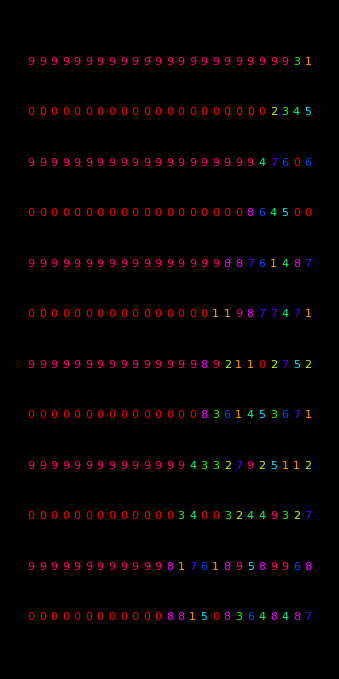

```mathematica
Clear[a,c,x,y,yy,n,m,k];
n=25;yy=10^n-1;
a=IntegerPart[4000/(Log[yy]//N)];
c=yy^a;
b=IntegerDigits[c];
Show[Graphics[Evaluate[
Table[Table[{Hue[Part[b,(y+25x)]/9.7],Text[Part[b,(y+25x)],{1.3y,-x}]},
{y,1,25}],{x,0,68}]]],AspectRatio->Automatic,Background->RGBColor[0,0,0],ImageSize ->{270,540}]
```

Example 2.  The following is the graph of the function  f(x)=-(xlog_10 x+(1-x)log_10(1-x)).  Please compare this to the figure in Example 1. It is not difficult to see the similarity between these two.

Mathematica code for Example 2.

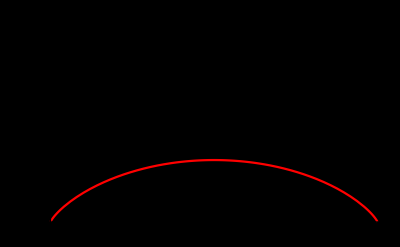

```mathematica
Plot[-(x*Log[10,x]+(1-x)*Log[10,1-x]),{x,0,1},PlotRange->{0,1},PlotStyle->RGBColor[1,0,0],Background->RGBColor[0,0,0]]
```

Theorem 1.  We expand (10^k-1)^nand express it as a matrix whose length of row is k. If we make n ⟶ ∞, then the figure made of numbers 1,2,3,4,5,6,7,8 is getting nearer and nearer to the graph of the function y = – (xlog_10x + (1–x)log_10(1–x)), where the x-coordinate is vertical.

For a proof see Theorem 1 in Miyadera [1].

Remark.  This result is closely related to the research about the expansion of (a+b)^n. See Miyadera [1], [2] and [3].

Example 3. We can make a beautiful movie using the figure in Example 1. Please look at the following table. We make the number X = 999...999 bigger, and at the same time we make the number Y smaller. In this way we keep the size of the number X^Y almost the same.
When we make a movie, we cut some part of the digits of the number.

Mathematica calculation for the following table.

```mathematica
Clear[aa,n,X,Y];
aa=Table[{x=10^n-1,y=IntegerPart[4000/Log[x]//N],Length[IntegerDigits[x^y]]},{n,1,25}];
FrameBox[GridBox[Join[{{"number X","number Y","the number of Digits of X^Y"}},aa],RowLines->True,ColumnLines->True]]//DisplayForm
```

number X | number Y | the number of Digits of X^Y
9 | 1820 | 1737
99 | 870 | 1737
999 | 579 | 1737
9999 | 434 | 1736
99999 | 347 | 1735
999999 | 289 | 1734
9999999 | 248 | 1736
99999999 | 217 | 1736
999999999 | 193 | 1737
9999999999 | 173 | 1730
99999999999 | 157 | 1727
999999999999 | 144 | 1728
9999999999999 | 133 | 1729
99999999999999 | 124 | 1736
999999999999999 | 115 | 1725
9999999999999999 | 108 | 1728
99999999999999999 | 102 | 1734
999999999999999999 | 96 | 1728
9999999999999999999 | 91 | 1729
99999999999999999999 | 86 | 1720
999999999999999999999 | 82 | 1722
9999999999999999999999 | 78 | 1716
99999999999999999999999 | 75 | 1725
999999999999999999999999 | 72 | 1728
9999999999999999999999999 | 69 | 1725

We make X bigger and Y smaller, and we make the graphics of the each number X^Y. Then we get the following movie.

Mathematica code for Example 3. You can make a movie by the following code. We omit the output because of the size of it.

```mathematica
Clear[a,c,b,x,y,n,m,k];
Do[yy=10^n-1;
a=IntegerPart[4000/(Log[yy]//N)];
c=yy^a;
b=IntegerDigits[c];
bb=Length[b];
Show[Graphics[{Text[SuperscriptBox[yy" ",a]//DisplayForm,{90,10},TextStyle->{FontSize->14}],Evaluate[
Table[Table[{Hue[Part[b,(y+25x)]/9.7],Text[Part[b,(y+25x)],{7y,-6x}]},
{y,1,25}],{x,0,64}]]}],AspectRatio->Automatic,Background->RGBColor[0,0,0],ImageSize ->{270,540}],{n,1,25}]
```

Example 4 (An open problem). Let x =

99999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999900000000000000000000000000000000000000000000000000000000000000000000000000000000899999999999999999999999999999999999999999999999999999999999999999999999999999, and

let y = 11. If you calculate the number x^y  and arrange it as the shape of a rectangle with the width of 80, then you get the following figure.
To study the mathematical structure of this number is an open problem.

Mathematica code for Example 4.

```mathematica
r=8;s=80;n=26;
yy=10^(12n+2)-10^(6n+2)+r*10^(3n-1)+10^(3n-1)-1;
a=IntegerPart[8000/(Log[yy]//N)];
b=IntegerDigits[yy^a];
bb=Length[b];
Print[yy];
Print[a];
Show[Graphics[Evaluate[
Table[Table[{Hue[Part[b,(y+(s)*x)]/9.7],Text[Part[b,(y+(s)*x)],{y,-x},TextStyle->{FontSlant->"Plain",FontSize->6}]},
{y,1,s}],{x,0,IntegerPart[bb/(s)]-1}]]],AspectRatio->Automatic,Background->RGBColor[0,0,0],ImageSize ->{640,350}]
```

Reference.

R.Miyadera, D.Minematsu and S.Hashiba [1], A beautiful figure made of 999...9, Visual Mathematics , Vol 6, No.2, 2006, Mathematical Institute of the Serbian Academy of Sciences and Arts.

http://www.mi.sanu.ac.yu/vismath/miyadera/999.html

R. Miyadera and Y. Kotera [2], Una Bella Curva Che Troviamo in Connessione con lo Sviluppo di  (a+b)^n Archimede 2/2005.

R. Miyadera [3], The curve of the expansion of (a + b)^n, Wolfram Information Center,

http://library.wolfram.com/infocenter/MathSource/5743/